```mathematica
f[x_]:= 2/(√π)x^0.5 Exp[-x];
g[x_]:= 0.5 Exp[-0.5 x];
```

```mathematica
c = FindMaximum[f[x]/g[x],{x,0.1} ][[1]];
```

```mathematica
xl[ll_]:= 1/(2(1-ll))
fg[x_,l_]:=(2 √x)/(√π*l) Exp[(l-1)x]
```

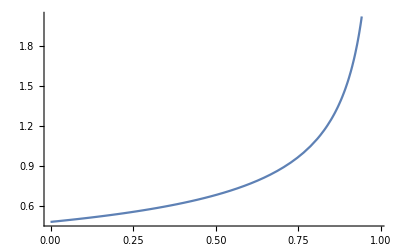

```mathematica
Plot[fg[xl[l],l],{l,0,0.99}]
```

```mathematica
fg[xl[ll],ll]
```

(ⅇ^((-1+ll)/(2 (1-ll))) √(1/(1-ll)) √(2/π))/ll

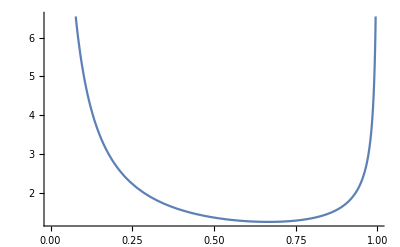

```mathematica
Plot[(ⅇ^((-1+ll)/(2 (1-ll))) √(1/(1-ll)) √(2/π))/ll,{ll,0,1}]
```

```mathematica
Solve[D[(ⅇ^((-1+ll)/(2 (1-ll))) √(1/(1-ll)) √(2/π))/ll,ll] == 0,ll]
```

{{ll→2/3}}

```mathematica
D[(ⅇ^((-1+ll)/(2 (1-ll))) √(1/(1-ll)) √(2/π))/ll,ll]
```

-(ⅇ^((-1+ll)/(2 (1-ll))) √(1/(1-ll)) √(2/π))/ll^2+(ⅇ^((-1+ll)/(2 (1-ll))) (1/(2 (1-ll))+(-1+ll)/(2 (1-ll)^2)) √(1/(1-ll)) √(2/π))/ll+(ⅇ^((-1+ll)/(2 (1-ll))) (1/(1-ll))^(3/2))/(ll √(2 π))

```mathematica
ll = 2/3
```

2/3

```mathematica
(ⅇ^((-1+ll)/(2 (1-ll))) √(1/(1-ll)) √(2/π))/ll
```

3 √(3/(2 ⅇ π))